```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/exptail_GW/math"];
```

## C

```mathematica
$Assumptions={q1>0,q2>0,k>0,uu1>0,uu2>0}
```

{q1>0,q2>0,k>0,uu1>0,uu2>0}

```mathematica
kk=k Transpose[{{0,0,1}}];
qq1=q1 Transpose[{{Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],Cos[θ1]}}];
qq2=q2 Transpose[{{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}}];
```

```mathematica
(Transpose[qq1].qq2)/k^2//Simplify
```

{{(q1 q2 (Cos[θ1] Cos[θ2]+Cos[ϕ1-ϕ2] Sin[θ1] Sin[θ2]))/k^2}}

```mathematica
u1=Sqrt[(Transpose[kk-qq1].(kk-qq1))[[1,1]]]/k//Simplify
v1=q1/k
u2=Sqrt[(Transpose[kk-qq2].(kk-qq2))[[1,1]]]/k//Simplify
v2=q2/k
wa=v1^2+v2^2-2((Transpose[qq1].qq2)[[1,1]])/k^2//Simplify
```

(√(k^2+q1^2-2 k q1 Cos[θ1]))/k

q1/k

(√(k^2+q2^2-2 k q2 Cos[θ2]))/k

q2/k

(q1^2+q2^2-2 q1 q2 Cos[θ1] Cos[θ2]-2 q1 q2 Cos[ϕ1] Cos[ϕ2] Sin[θ1] Sin[θ2]-2 q1 q2 Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2])/k^2

```mathematica
vcoord={u1,v1,ϕ1,u2,v2,ϕ2}/.{Cos[θ1]->c1,Sin[θ1]->Sqrt[1-c1^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2]}//Simplify
rcoord={q1,c1,ϕ1,q2,c2,ϕ2}
```

{(√(k^2-2 c1 k q1+q1^2))/k,q1/k,ϕ1,(√(k^2-2 c2 k q2+q2^2))/k,q2/k,ϕ2}

{q1,c1,ϕ1,q2,c2,ϕ2}

```mathematica
Jv=Table[D[vcoord[[j]], rcoord[[i]]],{i,6},{j,6}]//Simplify
```

{{(-c1 k+q1)/(k √(k^2-2 c1 k q1+q1^2)),1/k,0,0,0,0},{-q1/(√(k^2-2 c1 k q1+q1^2)),0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,(-c2 k+q2)/(k √(k^2-2 c2 k q2+q2^2)),1/k,0},{0,0,0,-q2/(√(k^2-2 c2 k q2+q2^2)),0,0},{0,0,0,0,0,1}}

```mathematica
Simplify[q1^2 q2^2/Det[Jv]/.{c1->(k^2+q1^2-k^2 uu1^2)/(2k q1),c2->(k^2+q2^2-k^2 uu2^2)/(2k q2)}]/.{q1->k vv1,q2->k vv2}
```

k^6 uu1 uu2 vv1 vv2

```mathematica
Clear[u1,v1,u2,v2]
```

```mathematica
s1=u1-v1;
t1=u1+v1-1;
s2=u2-v2;
t2=u2+v2-1;
```

```mathematica
scoord={s1,t1,s2,t2};
vcoord={u1,v1,u2,v2};
```

```mathematica
Jt=Table[D[scoord[[j]], vcoord[[i]]],{i,4},{j,4}]//Simplify
```

{{1,1,0,0},{-1,1,0,0},{0,0,1,1},{0,0,-1,1}}

```mathematica
Det[Jt]
```

4

```mathematica
Clear[s1,t1,s2,t2]
```

```mathematica
u2=(s2+t2+1)/2;
v2=(t2-s2+1)/2;
lncoord={Log[v2],Log[u2]}//Simplify
scoord={t2,s2};
```

{Log[1/2 (1-s2+t2)],Log[1/2 (1+s2+t2)]}

```mathematica
Jln=Table[D[lncoord[[j]], scoord[[i]]],{i,2},{j,2}]//Simplify
```

{{1/(1-s2+t2),1/(1+s2+t2)},{1/(-1+s2-t2),1/(1+s2+t2)}}

```mathematica
Det[Jln]/.{s2->u2-v2,t2->u2+v2-1}//Simplify
```

-2/(s2^2-(1+t2)^2)

### num

```mathematica
ϕ1-ϕ2/.{ϕ1->φ+ϕ2}//Simplify
```

φ

```mathematica
Cos[2ϕ1]Cos[2ϕ2]/.{ϕ1->φ+ϕ2}//TrigReduce
Sin[2ϕ1]Sin[2ϕ2]/.{ϕ1->φ+ϕ2}//TrigReduce
```

1/2 (Cos[2 φ]+Cos[2 φ+4 ϕ2])

1/2 (Cos[2 φ]-Cos[2 φ+4 ϕ2])

```mathematica
Cs=C/.Solve[wa^2==v1^2+v2^2-2v1 v2(S1 S2 C+C1 C2),C][[1]]/.{C1->(1-u1^2+v1^2)/(2v1),C2->(1-u2^2+v2^2)/(2v2)}/.{v2->kt^-1,u2->kt^-1,wa->kt^-1}//Simplify
```

(kt (-1+u1^2+v1^2))/(4 S1 S2 v1)

```mathematica
(v2 S2)^2/.{S2->Sqrt[1-C2^2]}/.{C2->(1-u2^2+v2^2)/(2v2)}/.{v2->kt^-1,u2->kt^-1}//Simplify
```

-1/4+1/kt^2

```mathematica
Simplify[1/(Sqrt[v1^2+v2^2-2v1 v2(S1 S2 C+C1 C2)]^3 Abs[D[Log[kt Sqrt[v1^2+v2^2-2v1 v2(S1 S2 C+C1 C2)]], C]])/.{C->Cs}/.{S2->Sqrt[1-C2^2]}/.{C1->(1-u1^2+v1^2)/(2v1),C2->(1-u2^2+v2^2)/(2v2)}/.{v2->kt^-1,u2->kt^-1}//Simplify,{kt>0,S1>0,v1>0,kt^2<4}]
```

(2 kt^2)/(√(4-kt^2) S1 v1)

```mathematica
IA[v_,u_]=(3(u^2+v^2-3))/(4 u^3 v^3);
IB[v_,u_]=-4u v+(v^2+u^2-3)Log[Abs[(3-(u+v)^2)/(3-(u-v)^2)]];
IC[v_,u_]=(v^2+u^2-3)UnitStep[u+v-Sqrt[3]];
```

```mathematica
Clear[Integrand]
```

```mathematica
Integrand[kt_,s1_,t1_]=1/(6π)u1 v1^2 S1 (2 Cs^2-1)/Sqrt[1-Cs^2] UnitStep[1-Abs[Cs]] kt^2 Sqrt[4-kt^2]UnitStep[2-kt]IA[v1,u1]IA[v2,u2](IB[v1,u1]IB[v2,u2]+π^2 IC[v1,u1]IC[v2,u2])/.{S1->Sqrt[1-C1^2],S2->Sqrt[1-C2^2]}/.{C1->(1-u1^2+v1^2)/(2v1),C2->(1-u2^2+v2^2)/(2v2)}/.{v2->kt^-1,u2->kt^-1}/.{u1->(s1+t1+1)/2,v1->(t1-s1+1)/2}//Simplify;//AbsoluteTiming
```

{39.3269,Null}

```mathematica
OGWinf[kt_]:=NIntegrate[Integrand[kt,s1,t1],{t1,0,∞},{s1,-1,1}]
OGW[kt_]:=NIntegrate[Integrand[kt,s1,t1],{t1,0,10^3},{s1,-1,1},MinRecursion->4]
```

```mathematica
OGWinf[0.03]//AbsoluteTiming
OGW[0.03]//AbsoluteTiming
```

{8.99794,0.13021}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.130196-0.0000161672 ⅈ and 0.0000155703 for the integral and error estimates.

{19.906,0.130196-0.0000161672 ⅈ}

```mathematica
OGWList=ParallelTable[{10^logk,Re[OGW[10^logk]//Quiet]},{logk,-2,Log10[2],10^-2}];//AbsoluteTiming
```

{2657.45,Null}

```mathematica
Export["C.dat",OGWList];
```

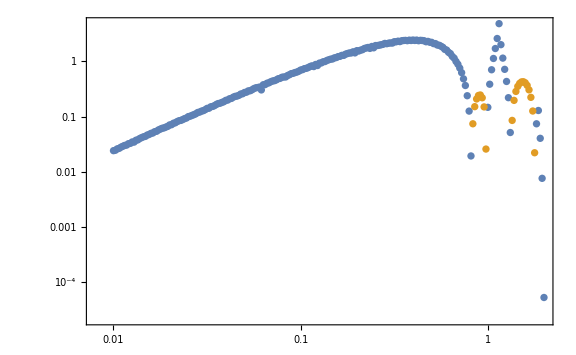

```mathematica
ListLogLogPlot[{Re[OGWList],Re[OGWList].{{1,0},{0,-1}}},Joined->False]
```

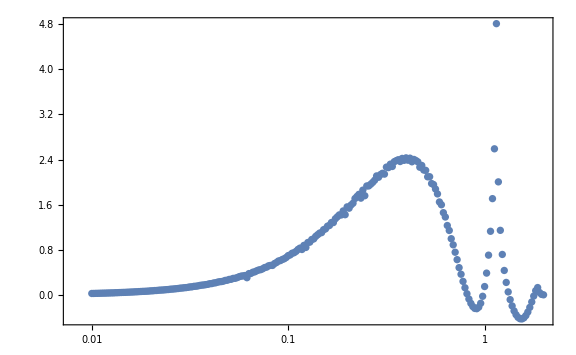

```mathematica
ListLogLinearPlot[OGWList,Joined->False,PlotRange->Full]
```

## Z hybrid

### Zh1

```mathematica
(* Simplify 用の条件 *)
$Assumptions={k>0,q1>0};
```

```mathematica
(* k は (0,0,k) の縦ベクトル *)
kk=Transpose[{{0,0,k}}];
```

```mathematica
(* q1, q2 の極座標. cosθ1 と q2 は制限されてる. ks = k* *)
qq1=q1 Transpose[{{Sqrt[1-c1^2]Cos[ϕ1],Sqrt[1-c1^2]Sin[ϕ1],c1}}]/.{c1->(k^2+q1^2-ks^2)/(2k q1)}//Simplify
qq2=ks Transpose[{{Sqrt[1-c2^2]Cos[ϕ2],Sqrt[1-c2^2]Sin[ϕ2],c2}}];
```

{{q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Cos[ϕ1]},{q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Sin[ϕ1]},{(k^2-ks^2+q1^2)/(2 k)}}

```mathematica
(* |k-q1| = ks となるかチェック *)
(Transpose[(kk-qq1)].(kk-qq1))//Simplify
```

{{ks^2}}

```mathematica
(* |q1-q2| と |k-q1+q2| *)
q1q2[k_,ks_,q1_,φ_,c2_]=Sqrt[(Transpose[(qq1-qq2)].(qq1-qq2))[[1,1]]/.{ϕ1->φ+ϕ2}]//Simplify
kq1q2[k_,ks_,q1_,φ_,c2_]=Sqrt[(Transpose[(kk-qq1+qq2)].(kk-qq1+qq2))[[1,1]]/.{ϕ1->φ+ϕ2}]//Simplify
```

√((-c2 ks (k^2-ks^2+q1^2)+k (ks^2+q1^2)-√(1-c2^2) ks √(-k^4-(ks^2-q1^2)^2+2 k^2 (ks^2+q1^2)) Cos[φ])/k)

√((ks (2 k ks+c2 (k^2+ks^2-q1^2)-√(1-c2^2) √(-k^4-(ks^2-q1^2)^2+2 k^2 (ks^2+q1^2)) Cos[φ]))/k)

```mathematica
(* 偏光テンソル *)
ep=1/Sqrt[2]{{1,0,0},{0,-1,0},{0,0,0}};
ec=1/Sqrt[2]{{0,1,0},{1,0,0},{0,0,0}};
```

```mathematica
(* Qλ が Adshead の表式と合うかチェック *)
qq=q Transpose[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}];
Transpose[qq].ep.qq//Simplify
Transpose[qq].ec.qq//Simplify
```

{{(q^2 Cos[2 ϕ] Sin[θ]^2)/(√2)}}

{{√2 q^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ]}}

```mathematica
(* QλQλ'. 変数を ϕ1, ϕ2 から φ = ϕ1 - ϕ2, ϕ2 に変更 *)
Qpp=(Transpose[qq1].ep.qq1)[[1,1]](Transpose[qq1-qq2].ep.(qq1-qq2))[[1,1]]/.{ϕ1->φ+ϕ2}//Simplify
Qcc=(Transpose[qq1].ec.qq1)[[1,1]](Transpose[qq1-qq2].ec.(qq1-qq2))[[1,1]]/.{ϕ1->φ+ϕ2}//Simplify
Qcp=(Transpose[qq1].ec.qq1)[[1,1]](Transpose[qq1-qq2].ep.(qq1-qq2))[[1,1]]/.{ϕ1->φ+ϕ2}//Simplify
Qpc=(Transpose[qq1].ep.qq1)[[1,1]](Transpose[qq1-qq2].ec.(qq1-qq2))[[1,1]]/.{ϕ1->φ+ϕ2}//Simplify
```

1/(32 k^4)(k^4+(ks^2-q1^2)^2-2 k^2 (ks^2+q1^2)) Cos[2 (φ+ϕ2)] (4 (-1+c2^2) k^2 ks^2 Cos[2 ϕ2]+(k^4+(ks^2-q1^2)^2-2 k^2 (ks^2+q1^2)) Cos[2 (φ+ϕ2)]+4 √(1-c2^2) k ks √(-k^4-(ks^2-q1^2)^2+2 k^2 (ks^2+q1^2)) Cos[φ+2 ϕ2])

2 q1^2 (1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Cos[φ+ϕ2] (-√(1-c2^2) ks Cos[ϕ2]+q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Cos[φ+ϕ2]) Sin[φ+ϕ2] (-√(1-c2^2) ks Sin[ϕ2]+q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Sin[φ+ϕ2])

q1^2 (1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Cos[φ+ϕ2] Sin[φ+ϕ2] ((√(1-c2^2) ks Cos[ϕ2]-q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Cos[φ+ϕ2])^2-(√(1-c2^2) ks Sin[ϕ2]-q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Sin[φ+ϕ2])^2)

-1/(16 k^2)(k^4+(ks^2-q1^2)^2-2 k^2 (ks^2+q1^2)) (-2 √(1-c2^2) ks Cos[ϕ2]+2 q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Cos[φ+ϕ2]) Cos[2 (φ+ϕ2)] (-2 √(1-c2^2) ks Sin[ϕ2]+2 q1 √(1-((k^2-ks^2+q1^2)^2)/(4 k^2 q1^2)) Sin[φ+ϕ2])

```mathematica
(* QλQλ' を ϕ2 について積分 *)
QppInt[k_,ks_,q1_,φ_,c2_]=Integrate[Qpp,{ϕ2,0,2π}]//Simplify
QccInt[k_,ks_,q1_,φ_,c2_]=Integrate[Qcc,{ϕ2,0,2π}]//Simplify
QcpInt[k_,ks_,q1_,φ_,c2_]=Integrate[Qcp,{ϕ2,0,2π}]//Simplify
QpcInt[k_,ks_,q1_,φ_,c2_]=Integrate[Qpc,{ϕ2,0,2π}]//Simplify
```

1/(32 k^4)π (k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1) ((k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1)+4 k ks (√(1-c2^2) √(-((k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1))) Cos[φ]+(-1+c2^2) k ks Cos[2 φ]))

1/(32 k^4)π (k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1) ((k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1)+4 k ks (√(1-c2^2) √(-((k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1))) Cos[φ]+(-1+c2^2) k ks Cos[2 φ]))

1/(8 k^3)ks π (k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1) (√(1-c2^2) √(-((k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1)))+2 (-1+c2^2) k ks Cos[φ]) Sin[φ]

-1/(8 k^3)ks π (k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1) (√(1-c2^2) √(-((k-ks-q1) (k+ks-q1) (k-ks+q1) (k+ks+q1)))+2 (-1+c2^2) k ks Cos[φ]) Sin[φ]

```mathematica
(* I^2 の時間平均を定義 *)
IA[p_,q_,k_]=3(p^2+q^2-3 k^2)/(4 p^3 q^3);
IB[p_,q_,k_]=-4p q+(p^2+q^2-3 k^2)Log[Abs[(3 k^2-(p+q)^2)/(3 k^2-(p-q)^2)]];
IC[p_,q_,k_]=π(p^2+q^2-3 k^2)UnitStep[p+q-Sqrt[3]k];
I2[k_,ks_,q1_,φ_,c2_]=1/2 IA[ks,q1,k]IA[kq1q2[k,ks,q1,φ,c2],q1q2[k,ks,q1,φ,c2],k](IB[ks,q1,k]IB[kq1q2[k,ks,q1,φ,c2],q1q2[k,ks,q1,φ,c2],k]+IC[ks,q1,k]IC[kq1q2[k,ks,q1,φ,c2],q1q2[k,ks,q1,φ,c2],k])//Simplify;//AbsoluteTiming
```

{34.8591,Null}

```mathematica
(* 被積分関数に Simplify をかけておく *)
IntegrandFpp[k_,ks_,q1_,φ_,c2_]=QppInt[k,ks,q1,φ,c2] I2[k,ks,q1,φ,c2] q1/q1q2[k,ks,q1,φ,c2]//Simplify;//AbsoluteTiming
IntegrandFpc[k_,ks_,q1_,φ_,c2_]=QpcInt[k,ks,q1,φ,c2] I2[k,ks,q1,φ,c2] q1/q1q2[k,ks,q1,φ,c2]//Simplify;//AbsoluteTiming
```

{155.521,Null}

{88.567,Null}

```mathematica
(* 真の被積分関数は三角不等式を満たしたときのみ上記の被積分関数で与えられるように場合分けで定義 *)
Clear[Integrandpp]
Integrandpp[k_,ks_,q1_,φ_,c2_]:=IntegrandFpp[k,ks,q1,φ,c2]/;(q1q2[k,ks,q1,φ,c2]<2ks)
Integrandpp[k_,ks_,q1_,φ_,c2_]:=0/;!(q1q2[k,ks,q1,φ,c2]<2ks)
Clear[Integrandpc]
Integrandpc[k_,ks_,q1_,φ_,c2_]:=IntegrandFpc[k,ks,q1,φ,c2]/;(q1q2[k,ks,q1,φ,c2]<2ks)
Integrandpc[k_,ks_,q1_,φ_,c2_]:=0/;!(q1q2[k,ks,q1,φ,c2]<2ks)
```

```mathematica
(* ΩGW を多重積分で定義. ks = 1 に固定 *)
Clear[OGWpp]
OGWpp[k_]:=k^2/π^2 NIntegrate[Integrandpp[k,1,q1,φ,c2],{q1,Abs[k-1],k+1},{φ,0,2π},{c2,-1,1}]
Clear[OGWpc]
OGWpc[k_]:=k^2/π^2 NIntegrate[Integrandpc[k,1,q1,φ,c2],{q1,Abs[k-1],k+1},{φ,0,2π},{c2,-1,1}]
```

```mathematica
(* どんなエラーが出るかチェック *)
OGWpp[1]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.61741 and 0.0844903 for the integral and error estimates.

{66.5403,0.163877}

```mathematica
(* 計算 *)
OGWppList=ParallelTable[{10^logk,OGWpp[10^logk]//Quiet},{logk,-2,Log10[3],1/100}];//AbsoluteTiming
OGWpcList=ParallelTable[{10^logk,OGWpc[10^logk]//Quiet},{logk,-2,Log10[3],1/100}];//AbsoluteTiming
```

{11103.7,Null}

{11680.1,Null}

```mathematica
(* 結果を出力 *)
Export["Zh1++.dat",OGWppList];
Export["Zh1+x.dat",OGWpcList];
```

```mathematica
(* 次回以降は計算せずデータを読み込めばよい *)
OGWppList=Import["Zh1++.dat"]//ToExpression;
OGWpcList=Import["Zh1+x.dat"]//ToExpression;
```

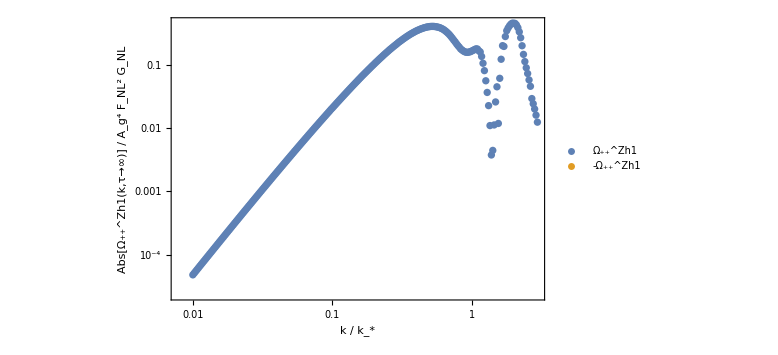

```mathematica
ListLogLogPlot[{OGWppList,OGWppList.{{1,0},{0,-1}}},Joined->False,FrameLabel->{Row[{k," / ",SubStar[k]}],Row[{Abs[(Subscript[Ω, "++"]^Zh1)[k,"τ→∞"]]," / ",Subscript[F, NL]^2 Subscript[G, NL] Subscript[A, g]^4}]},PlotLegends->Placed[{Subscript[Ω, "++"]^Zh1,-Subscript[Ω, "++"]^Zh1},{0.7,0.25}]]
```

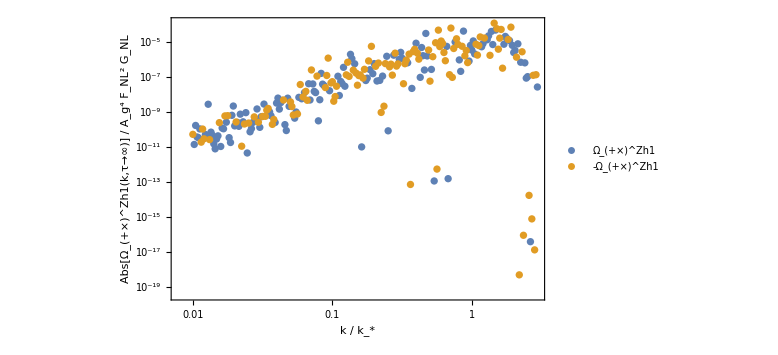

```mathematica
ListLogLogPlot[{OGWpcList,OGWpcList.{{1,0},{0,-1}}},Joined->False,FrameLabel->{Row[{k," / ",SubStar[k]}],Row[{Abs[(Subscript[Ω, "+×"]^Zh1)[k,"τ→∞"]]," / ",Subscript[F, NL]^2 Subscript[G, NL] Subscript[A, g]^4}]},PlotLegends->Placed[{Subscript[Ω, "+×"]^Zh1,-Subscript[Ω, "+×"]^Zh1},{0.2,0.2}]]
```

## CZ

```mathematica
2^3 2^2 3 2 4^2 1/(2π)^9(2 π^2)^4
```

96/π

```mathematica
$Assumptions={ks>0,k>0,q>0,0<q/(2ks)<1,-1<(q^2+k^2-ks^2)/(2q k)<1,0<ck^2<1,0<c2^2<1,0<c3p^2<1};
```

```mathematica
RθkT={{Cos[θk],0,-Sin[θk]},{0,1,0},{Sin[θk],0,Cos[θk]}};RθkT//MatrixForm
RϕkT={{Cos[ϕk],Sin[ϕk],0},{-Sin[ϕk],Cos[ϕk],0},{0,0,1}};RϕkT//MatrixForm
Rϕk=Transpose[RϕkT];Rϕk//MatrixForm
```

(Cos[θk] | 0 | -Sin[θk]
0 | 1 | 0
Sin[θk] | 0 | Cos[θk])

(Cos[ϕk] | Sin[ϕk] | 0
-Sin[ϕk] | Cos[ϕk] | 0
0 | 0 | 1)

(Cos[ϕk] | -Sin[ϕk] | 0
Sin[ϕk] | Cos[ϕk] | 0
0 | 0 | 1)

```mathematica
Rϕk.RθkT.RϕkT//Simplify
```

{{Cos[θk] Cos[ϕk]^2+Sin[ϕk]^2,(-1+Cos[θk]) Cos[ϕk] Sin[ϕk],-Cos[ϕk] Sin[θk]},{(-1+Cos[θk]) Cos[ϕk] Sin[ϕk],Cos[ϕk]^2+Cos[θk] Sin[ϕk]^2,-Sin[θk] Sin[ϕk]},{Cos[ϕk] Sin[θk],Sin[θk] Sin[ϕk],Cos[θk]}}

```mathematica
kk=k Transpose[{{Sin[θk]Cos[ϕk],Sin[θk]Sin[ϕk],Cos[θk]}}];
```

```mathematica
Rϕk.RθkT.RϕkT.kk//Simplify
```

{{0},{0},{k}}

```mathematica
pp=Transpose[{{-1,1,1}}];
```

```mathematica
RϕkT.pp/.{ϕk->π/2}
RθkT.RϕkT.pp/.{ϕk->π/2,θk->π/2}
Rϕk.RθkT.RϕkT.pp/.{ϕk->π/2,θk->π/2}
```

{{1},{1},{1}}

{{-1},{1},{1}}

{{-1},{-1},{1}}

```mathematica
Rϕk.RθkT.RϕkT/.{ϕk->π/2,θk->π/2}//MatrixForm
```

(1 | 0 | 0
0 | 0 | -1
0 | 1 | 0)

```mathematica
RθkT.RϕkT/.{ϕk->π/2,θk->π/2}//MatrixForm
```

(0 | 0 | -1
-1 | 0 | 0
0 | 1 | 0)

```mathematica
Rϕk/.{ϕk->π/2,θk->π/2}//MatrixForm
```

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

```mathematica
qq1=Transpose[{{q1x,q1y,q1z}}];
qq2=Transpose[{{q2x,q2y,q2z}}];
qq3=Transpose[{{q3x,q3y,q3z}}];
qq=qq1+qq2-qq3;
qq3p=qq3-qq2;
```

```mathematica
coord1=Join[Flatten[qq1],Flatten[qq2],Flatten[qq3]]
coord2=Join[Flatten[qq],Flatten[qq2],Flatten[qq3p]]
```

{q1x,q1y,q1z,q2x,q2y,q2z,q3x,q3y,q3z}

{q1x+q2x-q3x,q1y+q2y-q3y,q1z+q2z-q3z,q2x,q2y,q2z,-q2x+q3x,-q2y+q3y,-q2z+q3z}

```mathematica
JJ=Table[D[coord2[[i]], coord1[[j]]],{i,9},{j,9}]//Simplify
```

{{1,0,0,1,0,0,-1,0,0},{0,1,0,0,1,0,0,-1,0},{0,0,1,0,0,1,0,0,-1},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,-1,0,0,1,0,0},{0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,-1,0,0,1}}

```mathematica
Det[JJ]
```

1

```mathematica
qq=q Transpose[{{0,0,1}}];
qq2=q2 Transpose[{{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}}];
qq3p=q3p Transpose[{{Sin[θ3p]Cos[ϕ3p],Sin[θ3p]Sin[ϕ3p],Cos[θ3p]}}];
```

```mathematica
qqt=Rϕk.RθkT.RϕkT.qq/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
qq2t=Rϕk.RθkT.RϕkT.qq2/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
qq3pt=Rϕk.RθkT.RϕkT.qq3p/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
```

{{-√(1-ck^2) q Cos[ϕk]},{-√(1-ck^2) q Sin[ϕk]},{ck q}}

{{q2 (-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2))},{q2 (-c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2))},{q2 (c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk])}}

{{q3p (-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2))},{q3p (-c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2))},{q3p (c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk])}}

```mathematica
xcoord=Join[Flatten[qqt],Flatten[qq2t],Flatten[qq3pt]]
rcoord={q,ck,ϕk,q2,c2,ϕ2,q3p,c3p,ϕ3p}
```

{-√(1-ck^2) q Cos[ϕk],-√(1-ck^2) q Sin[ϕk],ck q,q2 (-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2)),q2 (-c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2)),q2 (c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk]),q3p (-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2)),q3p (-c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2)),q3p (c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk])}

{q,ck,ϕk,q2,c2,ϕ2,q3p,c3p,ϕ3p}

```mathematica
JJ=Table[D[xcoord[[i]], rcoord[[j]]],{i,9},{j,9}]//FullSimplify
```

{{-√(1-ck^2) Cos[ϕk],(ck q Cos[ϕk])/(√(1-ck^2)),√(1-ck^2) q Sin[ϕk],0,0,0,0,0,0},{-√(1-ck^2) Sin[ϕk],(ck q Sin[ϕk])/(√(1-ck^2)),-√(1-ck^2) q Cos[ϕk],0,0,0,0,0,0},{ck,q,0,0,0,0,0,0,0},{0,q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Cos[ϕk],q2 (√(1-c2^2) (-1+ck) Sin[ϕ2-2 ϕk]+c2 √(1-ck^2) Sin[ϕk]),-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2),-(q2 (c2 (1+ck) Cos[ϕ2]+c2 (-1+ck) Cos[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c2^2)),-1/2 √(1-c2^2) q2 ((1+ck) Sin[ϕ2]+(-1+ck) Sin[ϕ2-2 ϕk]),0,0,0},{0,q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Sin[ϕk],q2 (√(1-c2^2) (-1+ck) Cos[ϕ2-2 ϕk]-c2 √(1-ck^2) Cos[ϕk]),1/2 √(1-c2^2) ((1+ck) Sin[ϕ2]-(-1+ck) Sin[ϕ2-2 ϕk])-c2 √(1-ck^2) Sin[ϕk],-(q2 (c2 (1+ck) Sin[ϕ2]-c2 (-1+ck) Sin[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c2^2)),1/2 √(1-c2^2) q2 ((1+ck) Cos[ϕ2]-(-1+ck) Cos[ϕ2-2 ϕk]),0,0,0},{0,q2 (c2-(√(1-c2^2) ck Cos[ϕ2-ϕk])/(√(1-ck^2))),√(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk],c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk],q2 (ck-(c2 √(1-ck^2) Cos[ϕ2-ϕk])/(√(1-c2^2))),-√(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk],0,0,0},{0,q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Cos[ϕk],q3p (√(1-c3p^2) (-1+ck) Sin[ϕ3p-2 ϕk]+c3p √(1-ck^2) Sin[ϕk]),0,0,0,-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2),-(q3p (c3p (1+ck) Cos[ϕ3p]+c3p (-1+ck) Cos[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c3p^2)),-1/2 √(1-c3p^2) q3p ((1+ck) Sin[ϕ3p]+(-1+ck) Sin[ϕ3p-2 ϕk])},{0,q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Sin[ϕk],q3p (√(1-c3p^2) (-1+ck) Cos[ϕ3p-2 ϕk]-c3p √(1-ck^2) Cos[ϕk]),0,0,0,1/2 √(1-c3p^2) ((1+ck) Sin[ϕ3p]-(-1+ck) Sin[ϕ3p-2 ϕk])-c3p √(1-ck^2) Sin[ϕk],-(q3p (c3p (1+ck) Sin[ϕ3p]-c3p (-1+ck) Sin[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c3p^2)),1/2 √(1-c3p^2) q3p ((1+ck) Cos[ϕ3p]-(-1+ck) Cos[ϕ3p-2 ϕk])},{0,q3p (c3p-(√(1-c3p^2) ck Cos[ϕ3p-ϕk])/(√(1-ck^2))),√(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk],0,0,0,c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk],q3p (ck-(c3p √(1-ck^2) Cos[ϕ3p-ϕk])/(√(1-c3p^2))),-√(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk]}}

```mathematica
Det[JJ]//Simplify
```

-q^2 q2^2 q3p^2

```mathematica
ep={{1,0,0},{0,-1,0},{0,0,0}};
ec={{0,1,0},{1,0,0},{0,0,0}};
Tr[ep]
Tr[ec]
```

0

0

```mathematica
pp=Transpose[{{px,py,pz}}];
```

```mathematica
Transpose[pp].ep.pp
Transpose[pp].ec.pp
```

{{px^2-py^2}}

{{2 px py}}

```mathematica
(Transpose[Rϕk.RθkT.RϕkT.pp].ep.Rϕk.RθkT.RϕkT.pp)[[1,1]]//FullSimplify
```

(px-py) (px+py) Cos[θk/2]^4-4 px pz Cos[θk/2]^3 Cos[ϕk] Sin[θk/2]+(px-py) (px+py) Cos[4 ϕk] Sin[θk/2]^4-1/2 (px^2+py^2-2 pz^2) Cos[2 ϕk] Sin[θk]^2+4 py pz Cos[θk/2]^3 Sin[θk/2] Sin[ϕk]+2 py pz Sin[θk/2]^2 Sin[θk] Sin[3 ϕk]+2 px py Sin[θk/2]^4 Sin[4 ϕk]+px pz Csc[3 ϕk] Sin[θk/2]^2 Sin[θk] Sin[6 ϕk]

```mathematica
(Transpose[Rϕk.RθkT.RϕkT.pp].ec.Rϕk.RθkT.RϕkT.pp)[[1,1]]//FullSimplify
```

-2 py Cos[ϕk]^3 (pz Sin[θk]+py Sin[ϕk])+Cos[θk]^2 (px Cos[ϕk]+py Sin[ϕk])^2 Sin[2 ϕk]+(pz^2 Sin[θk]^2+py pz Sin[θk] Sin[ϕk]-px^2 Sin[ϕk]^2) Sin[2 ϕk]+px py Sin[2 ϕk]^2-2 Cos[θk] (px Cos[ϕk]+py Sin[ϕk]) (Cos[2 ϕk] (-py Cos[ϕk]+px Sin[ϕk])+pz Sin[θk] Sin[2 ϕk])+px pz Sin[θk] (-Sin[ϕk]+Sin[3 ϕk])

```mathematica
qq1=Transpose[{{q3p Sin[θ3p]Cos[ϕ3p],q3p Sin[θ3p]Sin[ϕ3p],q+q3p Cos[θ3p]}}]
qq2=q2 Transpose[{{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}}]
kk=k Transpose[{{Sin[θk]Cos[ϕk],Sin[θk]Sin[ϕk],Cos[θk]}}]
```

{{q3p Cos[ϕ3p] Sin[θ3p]},{q3p Sin[θ3p] Sin[ϕ3p]},{q+q3p Cos[θ3p]}}

{{q2 Cos[ϕ2] Sin[θ2]},{q2 Sin[θ2] Sin[ϕ2]},{q2 Cos[θ2]}}

{{k Cos[ϕk] Sin[θk]},{k Sin[θk] Sin[ϕk]},{k Cos[θk]}}

```mathematica
Transpose[qq2].qq2//Simplify
```

{{q2^2}}

```mathematica
Qp1=(Transpose[Rϕk.RθkT.RϕkT.qq1].ep.Rϕk.RθkT.RϕkT.qq1)[[1,1]]/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify;//AbsoluteTiming
Qc1=(Transpose[Rϕk.RθkT.RϕkT.qq1].ec.Rϕk.RθkT.RϕkT.qq1)[[1,1]]/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify;//AbsoluteTiming
Qp2=(Transpose[Rϕk.RθkT.RϕkT.qq2].ep.Rϕk.RθkT.RϕkT.qq2)[[1,1]]/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify;//AbsoluteTiming
Qc2=(Transpose[Rϕk.RθkT.RϕkT.qq2].ec.Rϕk.RθkT.RϕkT.qq2)[[1,1]]/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify;//AbsoluteTiming
```

{31.7301,Null}

{13.9453,Null}

{4.16846,Null}

{4.97442,Null}

```mathematica
(Transpose[kk-qq1].(kk-qq1))[[1,1]]/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify
```

k^2+q^2+q3p^2+2 q3p Cos[θ3p] (q-k Cos[θk])-2 k (q Cos[θk]+q3p Cos[ϕ3t] Sin[θ3p] Sin[θk])

```mathematica
(Transpose[kk-qq2].(kk-qq2))[[1,1]]/.{ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}//FullSimplify
```

k^2+q2^2-2 k q2 (Cos[θ2] Cos[θk]+Cos[ϕ2t] Sin[θ2] Sin[θk])

```mathematica
Qcc=Collect[Qc1 Qc2,Cos[2ϕk],Simplify];//AbsoluteTiming
Qcp=Collect[Qc1 Qp2,Cos[2ϕk],Simplify];//AbsoluteTiming
Qpc=Collect[Qp1 Qc2,Cos[2ϕk],Simplify];//AbsoluteTiming
Qpp=Collect[Qp1 Qp2,Cos[2ϕk],Simplify];//AbsoluteTiming
```

{16.5424,Null}

{27.7101,Null}

{27.305,Null}

{15.8173,Null}

```mathematica
ConstTrans={Cos[θk]->(q^2+k^2-ks^2)/(2q k),Sin[θk]->Sqrt[1-((q^2+k^2-ks^2)/(2q k))^2],Cos[θ2]->q/(2ks),Sin[θ2]->Sqrt[1-(q/(2ks))^2],q2->ks,q3p->ks,Cos[θ3p]->c3,Sin[θ3p]->Sqrt[1-c3^2],ϕ2->ϕ2t+ϕk,ϕ3p->ϕ3t+ϕk}/.{ks->1}
```

{Cos[θk]→(-1+k^2+q^2)/(2 k q),Sin[θk]→√(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)),Cos[θ2]→q/2,Sin[θ2]→√(1-q^2/4),q2→1,q3p→1,Cos[θ3p]→c3,Sin[θ3p]→√(1-c3^2),ϕ2→ϕ2t+ϕk,ϕ3p→ϕ3t+ϕk}

```mathematica
QccR[k_,q_,ϕ2t_,c3_,ϕ3t_]=Simplify[TrigExpand[Integrate[Qcc,{ϕk,0,2π}]]/.ConstTrans];//AbsoluteTiming
QcpR[k_,q_,ϕ2t_,c3_,ϕ3t_]=Simplify[TrigExpand[Integrate[Qcp,{ϕk,0,2π}]]/.ConstTrans];//AbsoluteTiming
QpcR[k_,q_,ϕ2t_,c3_,ϕ3t_]=Simplify[TrigExpand[Integrate[Qpc,{ϕk,0,2π}]]/.ConstTrans];//AbsoluteTiming
QppR[k_,q_,ϕ2t_,c3_,ϕ3t_]=Simplify[TrigExpand[Integrate[Qpp,{ϕk,0,2π}]]/.ConstTrans];//AbsoluteTiming
```

{113.811,Null}

{34.7698,Null}

{18.259,Null}

{111.439,Null}

```mathematica
kq1[k_,q_,c3_,ϕ3t_]=Sqrt[(Transpose[kk-qq1].(kk-qq1))[[1,1]]]/.ConstTrans//Simplify
kq2[k_,q_,ϕ2t_]=Sqrt[(Transpose[kk-qq2].(kk-qq2))[[1,1]]]/.ConstTrans//Simplify
q1[q_,c3_]=Sqrt[(Transpose[qq1].qq1)[[1,1]]]/.ConstTrans//Simplify
```

√(2+(c3 (1-k^2+q^2))/q-√(1-c3^2) k √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2)) Cos[ϕ3t])

(√(3+k^2-q^2-k √(4-q^2) √(-(k^4+(-1+q^2)^2-2 k^2 (1+q^2))/(k^2 q^2)) Cos[ϕ2t]))/(√2)

√(1+2 c3 q+q^2)

```mathematica
I2bar[p1_,q1_,p2_,q2_,k_]=1/2(3(p1^2+q1^2-3 k^2))/(4 p1^3 q1^3)(3(p2^2+q2^2-3 k^2))/(4 p2^3 q2^3)((-4p1 q1+(p1^2+q1^2-3 k^2)Log[Abs[(3 k^2-(p1+q1)^2)/(3 k^2-(p1-q1)^2)]])(-4p2 q2+(p2^2+q2^2-3 k^2)Log[Abs[(3 k^2-(p2+q2)^2)/(3 k^2-(p2-q2)^2)]])
+π^2(p1^2+q1^2-3 k^2)(p2^2+q2^2-3 k^2)UnitStep[p1+q1-Sqrt[3]k,p2+q2-Sqrt[3]k])//Simplify;
```

```mathematica
PppIntegrand[k_,q_,ϕ2t_,c3_,ϕ3t_]=QppR[k,q,ϕ2t,c3,ϕ3t]I2bar[kq1[k,q,c3,ϕ3t],q1[q,c3],kq2[k,q,ϕ2t],1,k];
PcpIntegrand[k_,q_,ϕ2t_,c3_,ϕ3t_]=QcpR[k,q,ϕ2t,c3,ϕ3t]I2bar[kq1[k,q,c3,ϕ3t],q1[q,c3],kq2[k,q,ϕ2t],1,k];
PpcIntegrand[k_,q_,ϕ2t_,c3_,ϕ3t_]=QpcR[k,q,ϕ2t,c3,ϕ3t]I2bar[kq1[k,q,c3,ϕ3t],q1[q,c3],kq2[k,q,ϕ2t],1,k];
PccIntegrand[k_,q_,ϕ2t_,c3_,ϕ3t_]=QccR[k,q,ϕ2t,c3,ϕ3t]I2bar[kq1[k,q,c3,ϕ3t],q1[q,c3],kq2[k,q,ϕ2t],1,k];
```

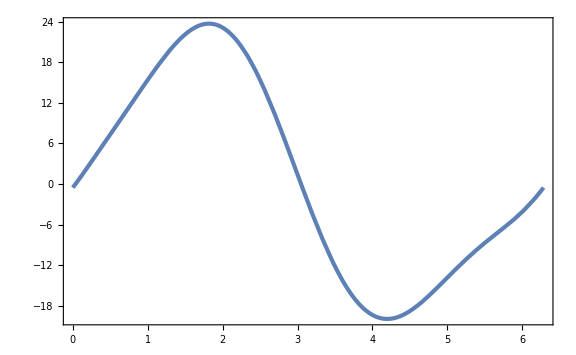

```mathematica
Plot[PccIntegrand[1/2,1,ϕ2t,-1/2,2π/3],{ϕ2t,0,2π},PlotRange->Full]
```

```mathematica
OGWpp[k_]:=1/π^2 k^2 NIntegrate[PppIntegrand[k,q,ϕ2t,c3,ϕ3t],{q,Abs[k-1],Min[2,k+1]},{ϕ2t,0,2π},{c3,-1,1},{ϕ3t,0,2π}]
OGWpc[k_]:=1/π^2 k^2 NIntegrate[PpcIntegrand[k,q,ϕ2t,c3,ϕ3t],{q,Abs[k-1],Min[2,k+1]},{ϕ2t,0,2π},{c3,-1,1},{ϕ3t,0,2π}]
OGWcp[k_]:=1/π^2 k^2 NIntegrate[PcpIntegrand[k,q,ϕ2t,c3,ϕ3t],{q,Abs[k-1],Min[2,k+1]},{ϕ2t,0,2π},{c3,-1,1},{ϕ3t,0,2π}]
OGWcc[k_]:=1/π^2 k^2 NIntegrate[PccIntegrand[k,q,ϕ2t,c3,ϕ3t],{q,Abs[k-1],Min[2,k+1]},{ϕ2t,0,2π},{c3,-1,1},{ϕ3t,0,2π}]
```

```mathematica
OGWppList=ParallelTable[{10^logk,OGWpp[10^logk]//Quiet},{logk,-1,Log10[3],10^-2}];//AbsoluteTiming
OGWpcList=ParallelTable[{10^logk,OGWpc[10^logk]//Quiet},{logk,-1,Log10[3],10^-2}];//AbsoluteTiming
OGWcpList=ParallelTable[{10^logk,OGWcp[10^logk]//Quiet},{logk,-1,Log10[3],10^-2}];//AbsoluteTiming
OGWccList=ParallelTable[{10^logk,OGWcc[10^logk]//Quiet},{logk,-1,Log10[3],10^-2}];//AbsoluteTiming
```

{485.558,Null}

{336.138,Null}

{335.743,Null}

{495.476,Null}

```mathematica
Export["CZ++.dat",OGWppList];
Export["CZ+x.dat",OGWpcList];
Export["CZx+.dat",OGWcpList];
Export["CZxx.dat",OGWccList];
```

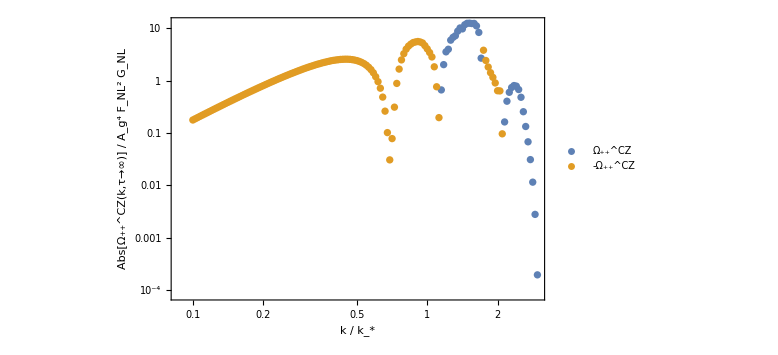

```mathematica
ListLogLogPlot[{OGWppList,OGWppList.{{1,0},{0,-1}}},Joined->False,FrameLabel->{Row[{k," / ",SubStar[k]}],Row[{Abs[(Subscript[Ω, "++"]^CZ)[k,"τ→∞"]]," / ",Subscript[F, NL]^2 Subscript[G, NL] Subscript[A, g]^4}]},PlotLegends->Placed[{Subscript[Ω, "++"]^CZ,-Subscript[Ω, "++"]^CZ},{0.2,0.2}]]
```

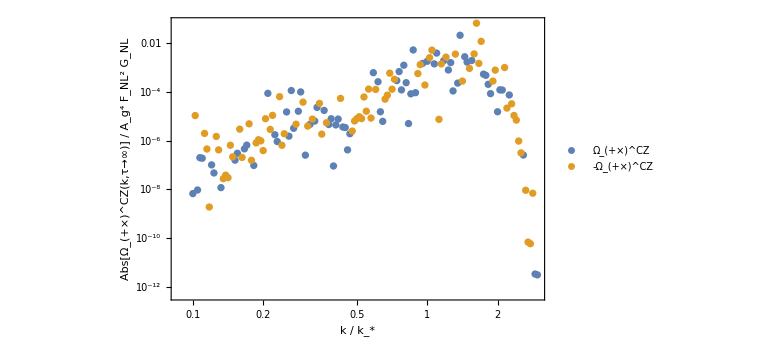

```mathematica
ListLogLogPlot[{OGWpcList,OGWpcList.{{1,0},{0,-1}}},Joined->False,FrameLabel->{Row[{k," / ",SubStar[k]}],Row[{Abs[(Subscript[Ω, "+×"]^CZ)[k,"τ→∞"]]," / ",Subscript[F, NL]^2 Subscript[G, NL] Subscript[A, g]^4}]},PlotLegends->Placed[{Subscript[Ω, "+×"]^CZ,-Subscript[Ω, "+×"]^CZ},{0.2,0.2}]]
```

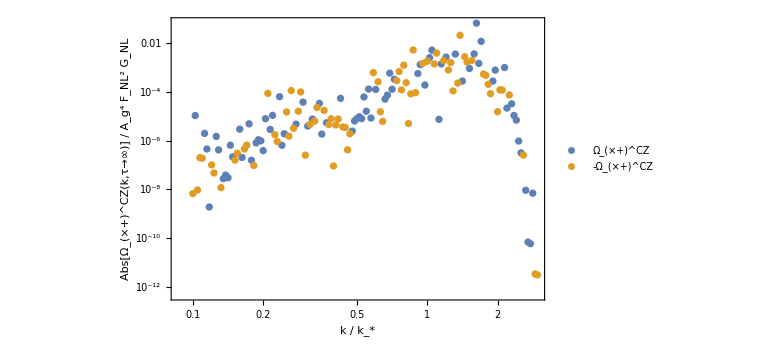

```mathematica
ListLogLogPlot[{OGWcpList,OGWcpList.{{1,0},{0,-1}}},Joined->False,FrameLabel->{Row[{k," / ",SubStar[k]}],Row[{Abs[(Subscript[Ω, "×+"]^CZ)[k,"τ→∞"]]," / ",Subscript[F, NL]^2 Subscript[G, NL] Subscript[A, g]^4}]},PlotLegends->Placed[{Subscript[Ω, "×+"]^CZ,-Subscript[Ω, "×+"]^CZ},{0.2,0.2}]]
```

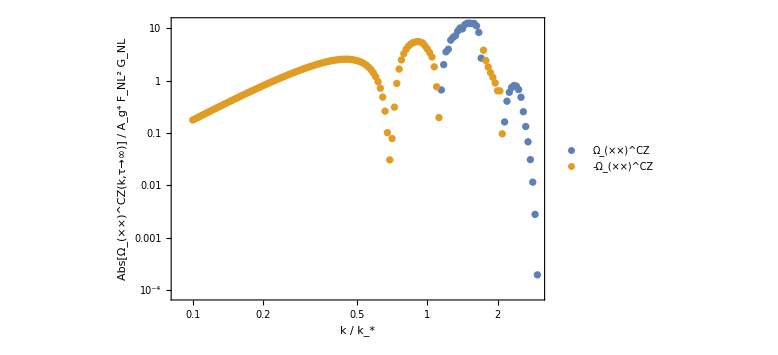

```mathematica
ListLogLogPlot[{OGWccList,OGWccList.{{1,0},{0,-1}}},Joined->False,FrameLabel->{Row[{k," / ",SubStar[k]}],Row[{Abs[(Subscript[Ω, "××"]^CZ)[k,"τ→∞"]]," / ",Subscript[F, NL]^2 Subscript[G, NL] Subscript[A, g]^4}]},PlotLegends->Placed[{Subscript[Ω, "××"]^CZ,-Subscript[Ω, "××"]^CZ},{0.2,0.2}]]
```